```mathematica
SetDirectory[NotebookDirectory[]];
boxLength=40;
stepInit=0;
stepFinal=9;
noMarkovChains=1;
timepointStart=160;
timepointEnd=165;
plots=ConstantArray[{},timepointEnd-timepointStart+1];
Do[
Do[
Do[
datav=Import["../data/cd_sampling/"<>IntegerString[timepoint,10,4]<>"_layer_0_"<>IntegerString[iChain,10,3]<>"_"<>IntegerString[step,10,2]<>".txt","Table"];
datah=Import["../data/cd_sampling/"<>IntegerString[timepoint,10,4]<>"_layer_1_"<>IntegerString[iChain,10,3]<>"_"<>IntegerString[step,10,2]<>".txt","Table"];
datavX=Select[datav,#[[3]]=="X"&];
datavY=Select[datav,#[[3]]=="Y"&];
datahX1=Select[datah,#[[3]]=="X1"&];
datahY1=Select[datah,#[[3]]=="Y1"&];
datav2=ConstantArray[0,{boxLength,boxLength}];
datah2=ConstantArray[0,{boxLength,boxLength}];
Do[
datav2[[pt[[1]],pt[[2]]]]=1;
,{pt,datavX}];
Do[
datav2[[pt[[1]],pt[[2]]]]=2;
,{pt,datavY}];
Do[
datah2[[pt[[1]],pt[[2]]]]=1;
,{pt,datahX1}];
Do[
datah2[[pt[[1]],pt[[2]]]]=2;
,{pt,datahY1}];
AppendTo[plots[[timepoint-timepointStart+1]],ArrayPlot[datav2,ColorRules->{1->Black,2->Blue,0->White},ImageSize->50]];
AppendTo[plots[[timepoint-timepointStart+1]],ArrayPlot[datah2,ColorRules->{1->Black,2->Red,0->White},ImageSize->50]];
,{step,stepInit,stepFinal}];
,{iChain,0,noMarkovChains-1}];
,{timepoint,timepointStart,timepointEnd}];
```

```mathematica
Grid[plots]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
stepInit=0;
stepFinal=50;
valsX=ConstantArray[{},timepointEnd-timepointStart+1];
valsY=ConstantArray[{},timepointEnd-timepointStart+1];
valsX1=ConstantArray[{},timepointEnd-timepointStart+1];
valsY1=ConstantArray[{},timepointEnd-timepointStart+1];
Do[
Do[
Do[
datav=Import["../data/cd_sampling/"<>IntegerString[timepoint,10,4]<>"_layer_0_"<>IntegerString[iChain,10,3]<>"_"<>IntegerString[step,10,2]<>".txt","Table"];
AppendTo[valsX[[timepoint-timepointStart+1]],Length[Select[datav,#[[3]]=="X"&]]];
AppendTo[valsY[[timepoint-timepointStart+1]],Length[Select[datav,#[[3]]=="Y"&]]];
,{step,stepInit,stepFinal}];
,{iChain,0,0}];
,{timepoint,timepointStart,timepointEnd}];
```

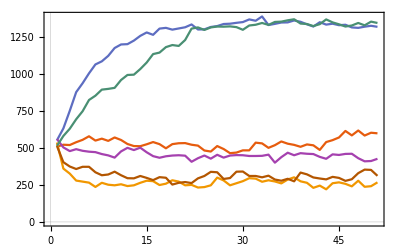
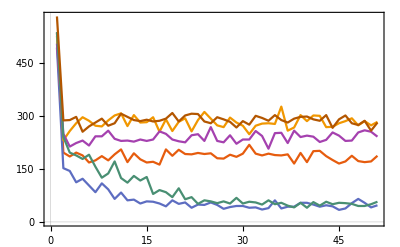

```mathematica
Row[{ListLinePlot[valsX],ListLinePlot[valsY]}]
```

## Calculate averages

```mathematica
SetDirectory[NotebookDirectory[]];
boxLength=40;
stepInit=0;
stepFinal=50-1;
noMarkovChains=10;
timepointStart=160;
timepointEnd=165;
valsXst=Association[];
valsYst=Association[];
valsXmean={};
valsYmean={};
Do[
valsX=ConstantArray[{},noMarkovChains];
valsY=ConstantArray[{},noMarkovChains];
Do[
Do[
datav=Import["../data/cd_sampling/"<>IntegerString[timepoint,10,4]<>"_layer_0_"<>IntegerString[iChain,10,3]<>"_"<>IntegerString[step,10,2]<>".txt","Table"];
AppendTo[valsX[[iChain+1]],Length[Select[datav,#[[3]]=="X"&]]];
AppendTo[valsY[[iChain+1]],Length[Select[datav,#[[3]]=="Y"&]]];
,{step,stepInit,stepFinal}];
,{iChain,0,noMarkovChains-1}];

AppendTo[valsXmean,Mean[valsX]];
AppendTo[valsYmean,Mean[valsY]];

valsXst[timepoint]=valsX;
valsYst[timepoint]=valsY;
,{timepoint,timepointStart,timepointEnd}];
```

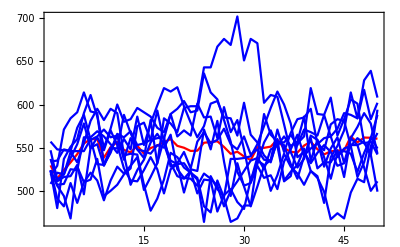

```mathematica
Show[ListLinePlot[valsXmean[[1]],PlotStyle->Red],ListLinePlot[valsXst[160],PlotStyle->Blue],PlotRange->All]
```

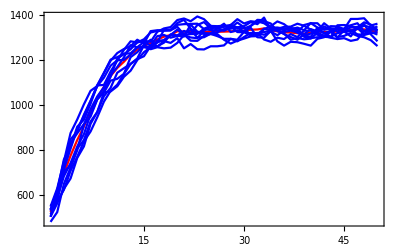

```mathematica
Show[ListLinePlot[valsXmean[[2]],PlotStyle->Red],ListLinePlot[valsXst[161],PlotStyle->Blue],PlotRange->All]
```

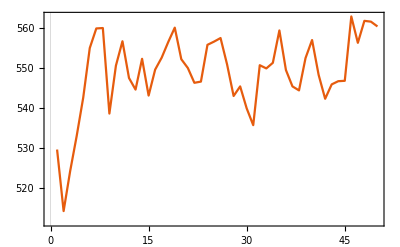
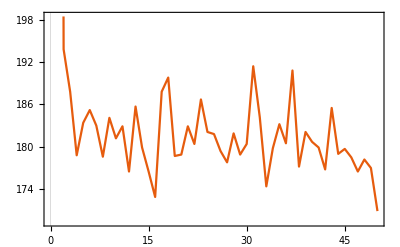

```mathematica
Row[{ListLinePlot[valsXmean],ListLinePlot[valsYmean]}]
```

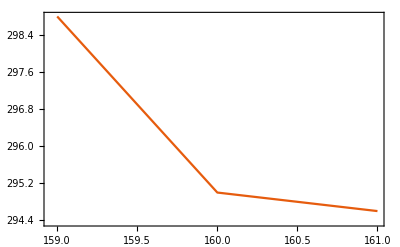

```mathematica
ListLinePlot[Transpose[{{159,160,161},valsXmean[[;;,-1]]}]]
```